```mathematica
(*Potencial*)
V[x_,a_]:=x^2+x^4+a x
```

```mathematica
Vtilde[x_,a_,ψ_,g_]:=V[x,a]+g Abs[ψ]^2
```

```mathematica
ψ0[x_]:=(1/π)^(1/4)Exp[-1/2 x^2]HermiteH[0,x]
```

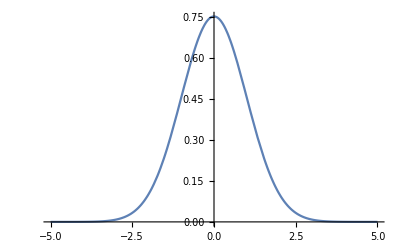

```mathematica
Plot[ψ0[x],{x,-5,5},PlotRange->All]
```

```mathematica
(*Rutina de Fourier calibrada*)
MiFourier[x_]:=Module[{pts=Length[x],maxValue,FT},
FT=Fourier[x];
maxValue=Max[Abs[Re[FT]]];
RotateLeft[FT/maxValue,pts/2]]
```

```mathematica
dt=0.01
```

0.01

```mathematica
ϕ=-ⅈ dt
```

0.-0.01 ⅈ

```mathematica
n=2^8;x0=-10.;xf=10;d=(xf-x0)/(n-1);
x=Range[x0,xf,d];
```

```mathematica
psi0=ψ0[x];
```

```mathematica
ψ1=Exp[ϕ/2 Vtilde[x,-1,psi0,1]]psi0;
```

```mathematica
ψ2=MiFourier[ψ1];
```

## Calibración de las ks

```mathematica
ψprueba[x_]:=Exp[- x^2]
```

```mathematica
ψprueba[x_]:=PDF[NormalDistribution[0,1],x]
```

```mathematica
ψprueba[0]
```

1

```mathematica
n=2^8;x0=-10.;xf=10;d=(xf-x0)/(n-1);
```

```mathematica
xprueba=Range[x0,xf,d];
```

```mathematica
xprueba//Length
```

256

```mathematica
yGauss=ψprueba[xprueba];
```

```mathematica
yFT=Abs[Re[MiFourier[yGauss]]];
```

```mathematica
ftMaxValue=Max[yFT];
```

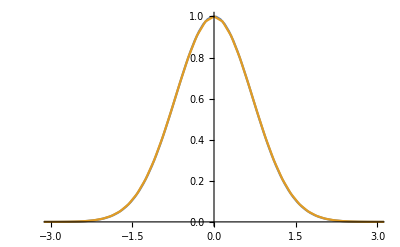

```mathematica
ListPlot[{Transpose[{xprueba,yGauss}],Transpose[{2xprueba-(xprueba[[2]]-xprueba[[1]]),yFT}]},PlotRange->{{-3,3},All},Joined->True]
```

```mathematica
yFTInverse=InverseFourier[yFT];
```

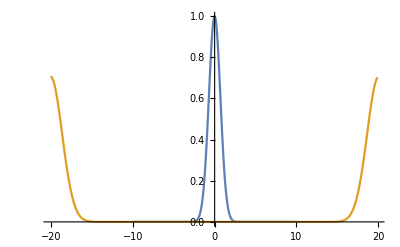

```mathematica
ListPlot[{Transpose[{xprueba,yGauss}],Transpose[{2xprueba-(xprueba[[2]]-xprueba[[1]]),Abs[Re[yFTInverse]]}]},PlotRange->Full,Joined->True]
```